```mathematica
SetDirectory[NotebookDirectory[]] ;
errors = Import["errors.dat"];
data = Import["solution.dat"];
dataquad = Import["solution_quad.dat"];
datasimple= Partition[#,2]&/@Import["solution_simple.dat"];
```

```mathematica
G[x_]:=2Exp[x];
```

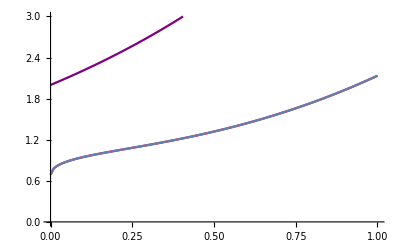

```mathematica
Show[ListLinePlot[dataquad,PlotStyle->Red,PlotRange->{{0,1},{0,3}}],ListLinePlot[Last@datasimple,PlotRange->{{0,1},{0,3}}],Plot[G[x],{x,0,1},PlotStyle->Purple,PlotRange->{{0,1},{0,3}}]]
```

```mathematica
(*eq={y[x]-λ∫_a^b k[x,s]*y[s]ⅆs==f[x]};
params = {a->0,b->1,k[x,s]->0.5(1-x *Cos[x *s]),f[x]->0.5(1+Sin[x])};
params1 = {a->0,b->1,k[x,s]->1,f[x]->0.5(1+Sin[x])};*)
```

```mathematica
(*eq=eq/.params;
DSolveValue[eq[[1]],y[x],x]*)
MaxNorm[data_,G_]:=Max[Table[Abs[G[data[[i,1]]]-data[[i,2]]],{i,1,Length@data}]];
```

```mathematica
errors2=Table[{i, MaxNorm[datasimple[[i]],G]},{i,1,Length@datasimple}];
```

```mathematica
logerrors=({#[[1]],Log[#[[2]]]})&/@errors2;
```

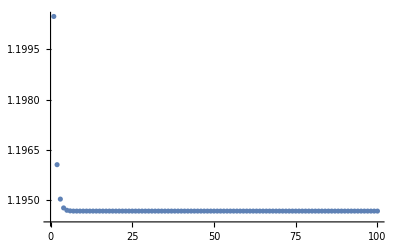

```mathematica
ListPlot[logerrors, PlotRange->Full]
```

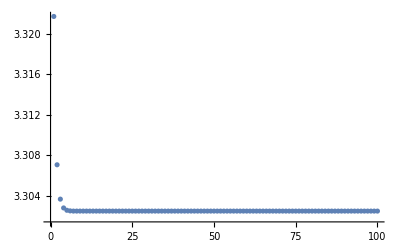

```mathematica
ListPlot[errors2, PlotRange->All]
```

```mathematica
Grid[{{"Iters","|err|"}}~Join~errors2, Frame->All, Spacings -> {1, 1}]
```

Iters | |err|
1 | 3.32172
2 | 3.30708
3 | 3.30369
4 | 3.30282
5 | 3.30259
6 | 3.30253
7 | 3.30251
8 | 3.30251
9 | 3.30251
10 | 3.30251
11 | 3.30251
12 | 3.30251
13 | 3.30251
14 | 3.30251
15 | 3.30251
16 | 3.30251
17 | 3.30251
18 | 3.30251
19 | 3.30251
20 | 3.30251
21 | 3.30251
22 | 3.30251
23 | 3.30251
24 | 3.30251
25 | 3.30251
26 | 3.30251
27 | 3.30251
28 | 3.30251
29 | 3.30251
30 | 3.30251
31 | 3.30251
32 | 3.30251
33 | 3.30251
34 | 3.30251
35 | 3.30251
36 | 3.30251
37 | 3.30251
38 | 3.30251
39 | 3.30251
40 | 3.30251
41 | 3.30251
42 | 3.30251
43 | 3.30251
44 | 3.30251
45 | 3.30251
46 | 3.30251
47 | 3.30251
48 | 3.30251
49 | 3.30251
50 | 3.30251
51 | 3.30251
52 | 3.30251
53 | 3.30251
54 | 3.30251
55 | 3.30251
56 | 3.30251
57 | 3.30251
58 | 3.30251
59 | 3.30251
60 | 3.30251
61 | 3.30251
62 | 3.30251
63 | 3.30251
64 | 3.30251
65 | 3.30251
66 | 3.30251
67 | 3.30251
68 | 3.30251
69 | 3.30251
70 | 3.30251
71 | 3.30251
72 | 3.30251
73 | 3.30251
74 | 3.30251
75 | 3.30251
76 | 3.30251
77 | 3.30251
78 | 3.30251
79 | 3.30251
80 | 3.30251
81 | 3.30251
82 | 3.30251
83 | 3.30251
84 | 3.30251
85 | 3.30251
86 | 3.30251
87 | 3.30251
88 | 3.30251
89 | 3.30251
90 | 3.30251
91 | 3.30251
92 | 3.30251
93 | 3.30251
94 | 3.30251
95 | 3.30251
96 | 3.30251
97 | 3.30251
98 | 3.30251
99 | 3.30251
100 | 3.30251

```mathematica
datah=Import["solution_h.dat"];
data2h=Import["solution_2h.dat"];
data4h=Import["solution_4h.dat"];
```

```mathematica
norms={{"h",MaxNorm[datah,G]},{"2h",MaxNorm[data2h,G]},{"4h",MaxNorm[data4h,G]}};
```

```mathematica
Grid[norms, Frame-> All, Spacings->{1, 1}]
```

h | 3.30252
2h | 3.30252
4h | 3.30251

#### Вырожденное ядро

```mathematica
datadegenerate =Flatten@ Import["solution_degenerate.dat"];
λ=1/2;
f [x_]:= √x+x^2;
```

```mathematica
Series[1-x*Cos[x*s],{x,0,20}]
```

1-x+(s^2 x^3)/2-(s^4 x^5)/24+(s^6 x^7)/720-(s^8 x^9)/40320+(s^10 x^11)/3628800-(s^12 x^13)/479001600+(s^14 x^15)/87178291200-(s^16 x^17)/20922789888000+(s^18 x^19)/6402373705728000+O[x]^21

```mathematica
Plot3D[{1-x,1-x+(s^2 x^3)/2,1-x+(s^2 x^3)/2-(s^4 x^5)/24,1-x+(s^2 x^3)/2-(s^4 x^5)/24+(s^6 x^7)/720-(s^8 x^9)/40320+(s^10 x^11)/3628800-(s^12 x^13)/479001600+(s^14 x^15)/87178291200-(s^16 x^17)/20922789888000+(s^18 x^19)/6402373705728000,1-x*Cos[x*s]},{x,0,1},{s,0,1}]
```

-Graphics3D-

```mathematica
u[x_]:=f[x]+λ*datadegenerate[[1]]+λ*Sum[datadegenerate[[i]]*(-1)^(i-1)x^(2i-3),{i,2,Length@datadegenerate}];
```

```mathematica
u[x]
```

0.68925+√x+x^2+1/2 (-1.3785 x+0.282941 x^3-0.0151971 x^5+0.00037566 x^7-5.34076×10^-6 x^9+4.93408×10^-8 x^11-3.2008×10^-10 x^13+1.53842×10^-12 x^15-5.69884×10^-15 x^17+1.67695×10^-17 x^19)

```mathematica
Sum[(-1)^(i-1)x^(2i-3),{i,2,Length@datadegenerate}]
```

-x+x^3-x^5+x^7-x^9+x^11-x^13+x^15-x^17+x^19

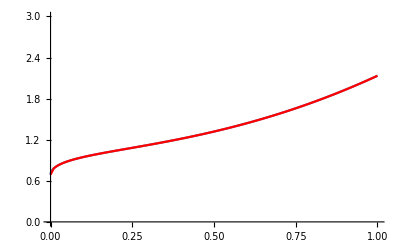

```mathematica
Show[Plot[u[x],{x,0,1},PlotRange->{{0,1},{0,3}}],ListLinePlot[dataquad,PlotStyle->Red,PlotRange->{{0,1},{0,3}}]]
```

#### Сингулярное ядро

```mathematica
datasingular = Import["solution_singular.dat"];
dataLOL=({#[[1]],#[[2]],-3})&/@datasingular;
exact=Table[2Sin[10ϕ],{ϕ,0,2π,(2π)/200}]//N;
Max[Table[Abs[exact[[i]]-datasingular[[i,3]]],{i,1,Length@datasingular}]]
```

3.98875×10^-6

```mathematica
Show[ListPointPlot3D[datasingular, AxesLabel->{"x", "y", "Res"},AxesOrigin->{0,0,0},PlotStyle->{Black,PointSize[0.007]}],
ListPointPlot3D[dataLOL, AxesLabel->{"x", "y", "Res"},AxesOrigin->{0,0,0}]/.Point[a___]:> {Thick,Line[a]},ParametricPlot3D[{Cos[ϕ],Sin[ϕ],2Sin[10ϕ]},{ϕ,0,2π},PlotStyle->{Red,Thin}]]
```

-Graphics3D-

```mathematica
{0,1/16,10/48,17/96,0}.{{1/2,1/2,0,0,0},{0,3/8,3/8,0,0},{0,0,1/4,1/4,0},{0,0,0,1/8,1/8},{0,0,0,0,0}}
```

{0,3/128,29/384,19/256,17/768}

```mathematica
Sum[{0,3/128,29/384,19/256,17/768}[[i]],{i,1,5}]
```

25/128